{725.653,55.0701,249.648}

{725.653,138.391,395.753}

0.349691

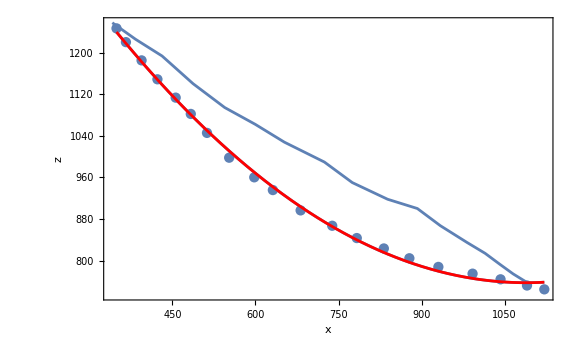

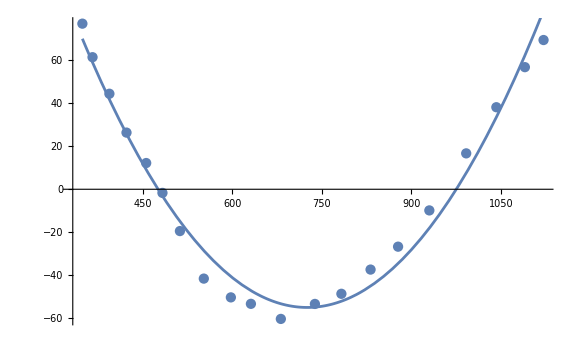

```mathematica
data=Import[NotebookDirectory[]<>"data/LandslideFailureSurfaces.xlsx"];
(*Extract first sheet*)
sheetdata=data[[13]];
(*Take rows 2 to end,first two columns*)
plotDataB=sheetdata[[2;;,1;;2]];  (*rows 2 to end,columns 1 and 2*)
plotDataH=sheetdata[[2;;,3;;4]];  (*rows 2 to end,columns 1 and 2*)

(*Function to do least squares and estimate shape of landslide base*)
IterativeLinearQuadraticVertexFit[pts_,maxIter_:10,tol_:10^-6]:=Module[{xData,zData,linFit,quadFit,residuals,newResiduals,i,change,a,b,c,A,B,C,vertexFit,fullFit},xData=pts[[All,1]];
zData=pts[[All,2]];
(*Initial linear fit*)
linFit=Fit[Transpose[{xData,zData}],{1,x},x];
change=Infinity;
i=0;
While[i<maxIter&&change>tol,i++;
(*Compute residuals*)
residuals=zData-(linFit/. x->xData);
(*Quadratic fit to residuals*)
quadFit=Fit[Transpose[{xData,residuals}],{1,x,x^2},x];
(*Update linear fit on corrected data*)
newResiduals=zData-(quadFit/. x->xData);
linFit=Fit[Transpose[{xData,newResiduals}],{1,x},x];
(*Measure change in fit*)
change=Max[Abs[newResiduals-residuals]];];
(*Extract coefficients of quadratic*)
a=Coefficient[quadFit,x,0];
b=Coefficient[quadFit,x,1];
c=Coefficient[quadFit,x,2];
(*Convert to vertex form A ((x-B)/C)^2-A*)
B=-b/(2 c);
A=b^2/(4 c)-a;
C=Sqrt[A/c];
vertexFit[x_]:=A*((x-B)/C)^2-A;
(*Full fitted function combining linear+vertex-form quadratic*)
fullFit[x_]:=(linFit/. x->x)+vertexFit[x];
<|"LinearFit"->linFit,"QuadFitCoeffs"->{a,b,c},
"VertexFit"->vertexFit,"VertexParams"->{B,A,C},"FullFit"->fullFit|>]

(*(*Plot*)
p1=ListLinePlot[plotDataB,
PlotStyle->{Red,Thick},(*line color and thickness*)
Frame->True,FrameLabel->{"x","z"},
GridLines->Automatic,ImageSize->Large];
p2=ListLinePlot[plotDataH,PlotStyle->{Black,PointSize[Large]},Frame->True,FrameLabel->{"Column 1","Column 2"},GridLines->Automatic,ImageSize->Large];
Show[p1,p2,PlotRange->Full,AspectRatio->1]*)

pts = plotDataB;
pts=Select[plotDataB,!AllTrue[#,#===""||#===Null&]&];(*data cleaning*)
(*pts={{x1,z1},{x2,z2},...}*)
xData=pts[[All,1]];
zData=pts[[All,2]];
fitResult=IterativeLinearQuadraticVertexFit[pts];
fitResult["VertexParams"]

linFit=Fit[Transpose[{xData,zData}],{1,x},x];
residuals=zData-(linFit/. x->xData);
quadFit=Fit[Transpose[{xData,residuals}],{1,x,x^2},x];
a=Coefficient[quadFit,x,0];  (*constant term*)
b=Coefficient[quadFit,x,1];  (*linear term*)
c=Coefficient[quadFit,x,2];  (*quadratic term*)
(*convert to form we care about*)
x0=-b/(2 c);
b0=b^2/(4 c)-a +quadFit/.x->x0+Max[Abs[xData-x0]];
Lx=Max[Abs[xData-x0]];(*Sqrt[x0/c];*)
{x0,b0,Lx}
b0/Lx

p1=ListPlot[{pts},Frame->True,FrameLabel->{"x","z"}];
p2=ListLinePlot[{plotDataH}];
p3=Plot[linFit+quadFit,{x,Min[xData],Max[xData]}];
p4=Plot[fitResult["FullFit"][x],{x,Min[pts[[All,1]]],Max[pts[[All,1]]]},PlotStyle->{Red}];
Show[p1,p2,p3,p4,ImageSize->Large,PlotRange->{Min[zData]-10,Max[zData]+10}]
p1=ListPlot[Transpose[{xData,residuals}]];
p3=Plot[quadFit,{x,Min[xData],Max[xData]}];
Show[p1,p3]
```